```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"share.m"
```

```mathematica
<<"mdata/real-1.mx";
<<"mdata/virtual-1.mx";
<<"mdata/subtraction-1.mx";
<<"mdata/counter-1.mx";
```

## useful functions and replacements

```mathematica
FastLimit[term_]:=Module[
{tablein=(term//Expand//Apply[List,#]&),tableout={},bad={},limit=0,limit2=0,i=0,finaloutput=0},
For[i=1,i≤(tablein//Length),i++,
limit=Quiet[Check[(tablein[[i]]//Together//ReplaceAll[#,s23->0]&),BAD]];
If[limit===BAD,
(*Print["bad at "<>ToString[i]<>"..."<>ToString[limit]];*)
bad=Append[bad,tablein[[i]]],
tableout=Append[tableout,limit]]
];
tableout=tableout//DeleteCases[#,0]&;
limit2=Check[(bad//Apply[Plus,#]&)//Limit[#,s23->0]&,BAD];
Print["Test limit: "<>ToString[(limit2//FullForm)]];
finaloutput=(tableout//Apply[Plus,#]&)+limit2;
finaloutput
];

MakeRulePoly[termlist_,factorto1list_]:=Module[
{

setto1=Table[factorto1list[[i]]->1,{i,1,factorto1list//Length}],
polyv1={},
polyv2={},
poly={},
rule={}
},

polyv1=termlist//ReplaceAll[#,setto1]&//Numerator//Times[#,YYY]&//Apply[List,#,1]&//Flatten//DeleteDuplicates//DeleteCases[#,_Integer|YYY]&;
(*polyv2=-polyv1//Simplify;
poly=Join[polyv1,polyv2]//DeleteDuplicates;*)
rule=polyv1//Table[If[(#[[i]]//Length)>2,#[[i]]->ToExpression["C"<>ToString[i]],Nothing],{i,1,#//Length}]&;
rule


];


ReverseRule[rulelist_]:=Table[rulelist[[i,2]]->rulelist[[i,1]],{i,1,rulelist//Length}];

(*term to list*)
SeparateTerm[log_,expr_]:=log//Expand//Collect[#,expr,Simplify]&//Apply[List,#]&//CollectSeparate[#,{E4Pi,Log4}]&//CollectSeparate[#,{sgnst}]&;
(*list to list*)
CollectSeparate[list_,exprlist_]:=list//Expand//Collect[#,exprlist,Simplify]&//Plus[#,XXX]&//Apply[List,#,1]&//ReplaceAll[#,XXX->0]&//Flatten//DeleteCases[#,0]&;

SimplifyLogTerm[log_]:=Module[
{list={},logsimple={}},
list=log//SeparateTerm[#,Log[__]]&;
AruleReverse=list//Cases[#,Log[x_]y_->x]&//DeleteDuplicates//Table[Log[#[[i]]]->Log[ToExpression["A"<>ToString[i]]],{i,1,#//Length}]&;
CruleReverse=list//MakeRulePoly[#,{Log[__],sgnst,E4Pi,Log4}]&;
Crule=Table[CruleReverse[[i,2]]->CruleReverse[[i,1]],{i,1,CruleReverse//Length}];
Arule=Table[AruleReverse[[i,2]]->AruleReverse[[i,1]],{i,1,AruleReverse//Length}];
list=list//ReplaceAll[#,AruleReverse]&;
logsimple=list//ReplaceAll[#,CruleReverse]&//ReplaceAll[#,Table[-CruleReverse[[i,1]]->-CruleReverse[[i,2]],{i,1,CruleReverse//Length}]]&//Apply[Plus,#]&//Collect[#,CruleReverse[[All,2]],FullSimplify]&

]

SimplifyDoubleLogTerm[doublelog_]:=Module[{list={}},
list=doublelog//Collect[#,{Log[x__]Log[x__],Log[x__]Log[y__]},Simplify]&//ReplaceAll[#,Log[x__]Log[y__]->1/2(Log[x]^2+Log[y]^2-Log[x/y]^2)]&//Expand//Collect[#,{Log[x__]Log[x__],Log[x__]Log[y__]},Simplify]&//Apply[List,#]&;
CruleReverse=list//MakeRulePoly[#,{Log[__]}]&;
Crule=Table[CruleReverse[[i,2]]->CruleReverse[[i,1]],{i,1,CruleReverse//Length}];

list//.CruleReverse//.Table[-CruleReverse[[i,1]]->-CruleReverse[[i,2]],{i,1,CruleReverse//Length}]//Apply[Plus,#]&//Collect[#,CruleReverse[[All,2]],Simplify]&

]

SimplifyPolyLogTerm[polylog_]:=Module[
{list={}},
list=polylog//Collect[#,PolyLog[_,_],Simplify]&//Apply[List,#]&;

CruleReverse=list//MakeRulePoly[#,{PolyLog[_,__]}]&;

Crule=Table[CruleReverse[[i,2]]->CruleReverse[[i,1]],{i,1,CruleReverse//Length}];

list//ReplaceAll[#,CruleReverse]&//ReplaceAll[#,Table[-CruleReverse[[i,1]]->-CruleReverse[[i,2]],{i,1,CruleReverse//Length}]]&//ReplaceAll[#,PolyLog[n_,x__]:>PolyLog[n,x/.Crule]]&//Apply[Plus,#]&//Collect[#,CruleReverse[[All,2]]]&

]

SimplifyRationalTerm[term_]:=Module[
{list={}},
list=rational//ReplaceAll[#,{√((s-τ)^2)->(s-τ) sgnst,Power[(s-τ)^2,-1/2]->(s-τ)^-1 sgnst}]&//Expand//Collect[#,{E4Pi,Log4,sgnst,π},Simplify]&//Apply[List,#]&;
CruleReverse=list//MakeRulePoly[#,{}]&;
Crule=Table[CruleReverse[[All,2]]->CruleReverse[[All,1]],{i,1,CruleReverse//Length}];

list=list//.CruleReverse//Apply[Plus,#]&;
list=list//.Table[-CruleReverse[[All,1]]->-CruleReverse[[All,2]],{i,1,CruleReverse//Length}]//Apply[Plus,#]&

]


Simple1[expr_]:=expr//Expand//Collect[#,{Log[x__]Log[x__],Log[x__]Log[y__],Log[__],PolyLog[__,__]},Simplify]&;



varreplace={

Q^p_->(υ+τ-s)^(p/2),
Q^p_->(-u-t-s)^(p/2),
t->-τ,
u->-υ,
μ^2->μ2,
Log[μ]->Log[μ2]/2,
EulerGamma->E4Pi+Log[4 π]
};

logargreplace1={

Log[x_]:>Log[Abs[x//Factor//Simplify]]
};
logargreplace2={

Log[Abs[x_ y_]]->Log[Abs[x]]+Log[Abs[y]],
Log[1/x_]->-Log[x]
};

logargreplace3={
Log[Abs[x_]]:>Log[Power[Abs[(x^2//Simplify)],1/2]]
};


logreplace={

Log[a_/b_]->Log[a]-Log[b],
Log[a_ Power[b_,p_]]->Log[a]+p Log[b],
Log[Power[a_,p_]]->p Log[a],
Log[n_Integer x__]->Log[n]+Log[x],
Log[Rational[a_,b_] x__]->Log[a]-Log[b]+Log[x],
Log[n_Integer π]->Log[n]+Log4π-Log4,
Log[n_Integer]:>Log4*Log[4,n],
Log[π]->Log4π-Log4
};

polylogargreplace={
PolyLog[n_,x_]:>PolyLog[n,x//Factor//Simplify]

};
```

## separation of terms

```mathematica
total=(realpiece-subtractionpiece+(virtualpiece[[1]]+virtualpiece[[2]]+virtualpiece[[3]]+virtualpiece[[4]]+counterpiece)δ[s23])//ReplaceAll[#,Subscript[C, MSB]->E4Pi]&//Expand;
```

```mathematica
deltaterms=total//Select[#,MatchQ[#,δ[__]__]&]&;
Plus1Bterms=total//Select[#,MatchQ[#,Plus1B[__]__]&]&;
Plus2Bterms=total//Select[#,MatchQ[#,Plus2B[__]__]&]&;
regularterms=total//Select[#,FreeQ[#,δ[__]__]&&FreeQ[#,Plus1B[__]__]&&FreeQ[#,Plus2B[__]__]&]&;
```

```mathematica
(total//Length)-(deltaterms//Length)-(Plus1Bterms//Length)-(Plus2Bterms//Length)-(regularterms//Length)
```

0

# δ terms

```mathematica
list=deltaterms//ReplaceAll[#,{δ[_]->1,g->1}]&//Expand//Apply[List];
```

```mathematica
list2=Table[Quiet[Check[ReplaceRepeated[list[[i]],s23->0],list[[i]]]],{i,1,list//Length}]//DeleteCases[#,0]&//Together;
```

```mathematica
list3=Table[Quiet[Check[ReplaceRepeated[list2[[i]],s23->0],list2[[i]]]],{i,1,list2//Length}]//DeleteCases[#,0]&;
```

```mathematica
deltatermslimit=list3//Apply[Plus]//Expand//ReplaceAll[#,s23->0]&;
```

```mathematica
deltatermss230=deltaterms//ReplaceAll[#,δ[_]->1]&//FastLimit
```

Test limit: 0

-(g^2 log^2((2 Q^2+s+t-√((s+t)^2))/(2 Q^2+s+t+√((s+t)^2))) s^9)/(1536 π^5 (Q^2+s+t) (s^2+2 t s+t^2)^(7/2))-(g^2 log(B) log((2 Q^2+s+t-√((s+t)^2))/(2 Q^2+s+t+√((s+t)^2))) s^9)/(768 π^5 (Q^2+s+t) (s^2+2 t s+t^2)^(7/2))+(g^2 log((2 Q^2+s+t-√((s+t)^2))/(2 Q^2+s+t+√((s+t)^2))) s^9)/(768 π^5 (Q^2+s+t) (s^2+2 t s+t^2)^(7/2) ϵ)-(ℽ g^2 log(1/1) s^9)/(768 π^5 (Q^2+s+t) (s^2+2 t s+t^2)^(7/2))+1/1+3541+1+(g^2 Q^4 t^4 log(2))/(128 π^5 1 1^2)-(5 g^2 t^8 log(2))/(3072 π^5 (-Q^2-s-t) (s^2+2 t s+t^2)^3)-(5 g^2 Q^2 t^7 log(2))/(768 π^5 (-Q^2-s-t) (s^2+2 t s+t^2)^3)-(5 g^2 Q^4 t^6 log(2))/(768 π^5 (-Q^2-s-t) (s^2+2 t s+t^2)^3)
 |  |  |  |

```mathematica
(deltatermss230-deltatermslimit)/.g->1//Collect[#,{Log[__]Log[__],Log[x__]Log[y__],Log[x__],PolyLog[_,_]},Simplify]&
```

0

```mathematica
list1=deltatermss230/.g->1//Expand//Select[#,FreeQ[#,ϵ^-1]&&FreeQ[#,ϵ^-2]&]&;
(*//Collect[#,{Log[x__]Log[y__],Log[x__]Log[x__],Log[x__],PolyLog[_,_]},Simplify]&;*)
```

```mathematica
list2=list1//Select[#,MatchQ[#,Log[__]__]&&FreeQ[#,Log[x__]Log[x__]__]&&FreeQ[#,Log[x__]Log[y__]__]&]&;
list3=list1//Select[#,MatchQ[#,Log[x__]Log[x__]__]||MatchQ[#,Log[x__]Log[y__]__]&]&;
list4=list1//Select[#,MatchQ[#,PolyLog[_,_]__]&]&;
list5=list1//Select[#,FreeQ[#,Log[__]__]&&FreeQ[#,Log[x__]Log[x__]__]&&FreeQ[#,Log[x__]Log[y__]__]&&FreeQ[#,PolyLog[_,_]__]&]&;
```

```mathematica
list1//Length
Table["list"<>ToString[i]<>"//Length",{i,2,5}]//ToExpression
%//Apply[Plus]
```

2078

{787,781,159,351}

2078

```mathematica
kintemp2={μ2->μ^2,Log4->Log[4],Log4π->Log[4 π],u->-t-s-Q^2,υ->-u,τ->-t,E4Pi->EulerGamma-Log[4π],Subscript[n, f]->4,s->(1-xh)/xh*Q^2,t->-(1-zh)*Q^2-zh*qT^2,g->1,xh->x/xi,zh->(Q^2*(1-xh)/xh)/(qT^2+Q^2*(1-xh)/xh),x->0.1326,z->0.4,Q->5.3^(0.5),qT->3,B->Q^2(1/xh-1)(1-z)-z*qT^2,μ->Q,gp->1,δ[_]->1};
```

```mathematica
list21=list2//Collect[#,Log[x__],Simplify]&;
list31=list3//Collect[#,{Log[x__]Log[x__],Log[x__]Log[y__]},Simplify]&//ReplaceAll[#,{Log[(2 (Q^2+s+t))/(2 Q^2+s+t+√((s+t)^2))] Log[(-s^2-t s)/(s √((s+t)^2))+1]->Log[2] Log[(Q^2+s+t)/Q^2]*(1-Abs[s+t]/(s+t))/2,Log[(2 (Q^2+s+t))/(2 Q^2+s+t+√((s+t)^2))] Log[(-t^2-s t)/(t √((s+t)^2))+1]->Log[2] Log[(Q^2+s+t)/Q^2]*(1-Abs[s+t]/(s+t))/2}]&;
```

```mathematica
list41=list4//Collect[#,{PolyLog[_,_]},Simplify]&//ReplaceAll[#,PolyLog[2,x__]:>PolyLog[2,x//Together]]&;
```

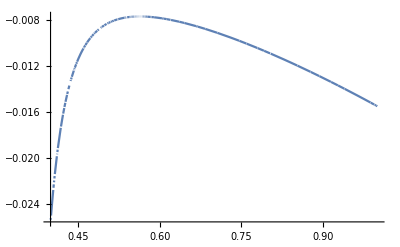

```mathematica
list51=list5//Simplify;



(*{list31}//.kintemp2//Plot[#,{xi,0.4,1.0},PlotRange->All]&*)
{list41}//.kintemp2//Plot[#,{xi,0.4,1.0},PlotRange->All]&
```

```mathematica
PolyLog[2,0]
```

0

```mathematica
temp41={
list41//Expand//Collect[#,PolyLog[_,_],Simplify]&//Simplify[#,s+t>0]&,
list41//Expand//Collect[#,PolyLog[_,_],Simplify]&//Simplify[#,s+t<0]&
};
sign41={1/2(1+Abs[s+t]/(s+t)),1/2(1-Abs[s+t]/(s+t))};

list42=temp41.sign41;
```

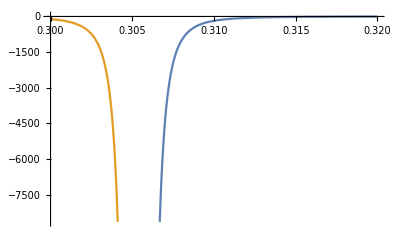

```mathematica
{temp41//.kintemp2}//Plot[#,{xi,0.3,0.32}]&
```

```mathematica
test2//Simplify
```

test2

```mathematica
test2=total//Expand//Select[#,FreeQ[#,ϵ^-1 __]&&MatchQ[#,Plus1B[_,_]__]&]&//ReplaceAll[#,{Plus1B[_,_]->1,g->1}]&;

test1=total//Expand//Select[#,FreeQ[#,ϵ^-1 __]&&MatchQ[#,Plus1B[_,_]__]&]&//ReplaceAll[#,{Plus1B[_,_]->1,g->1}]&//Apply[List];
```

$Aborted

```mathematica
test1regular=Table[Check[test1[[i]]//Together//ReplaceAll[#,s23->0]&,test1[[i]]],{i,test1//Length}]//DeleteCases[#,0]&//Apply[Plus]//Collect[#,{Log[__]},Simplify]&;
```

```mathematica
test1regularpos=test1regular//ReplaceRepeated[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//Simplify//Expand//Collect[#,Log[_],Simplify]&//Simplify[#,s+t>0]&
test1regularneg=test1regular//ReplaceRepeated[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//Simplify//Expand//Collect[#,Log[_],Simplify]&//Simplify[#,s+t<0]&
```

-(s (26 log(Abs[μ])-9 log(Abs[Q^2+s+t])+9 log(Abs[s])+9 log(Abs[t])+3))/(96 π^5)

-(s (26 log(Abs[μ])-9 log(Abs[Q^2+s+t])+9 log(Abs[s])+9 log(Abs[t])+3))/(96 π^5)

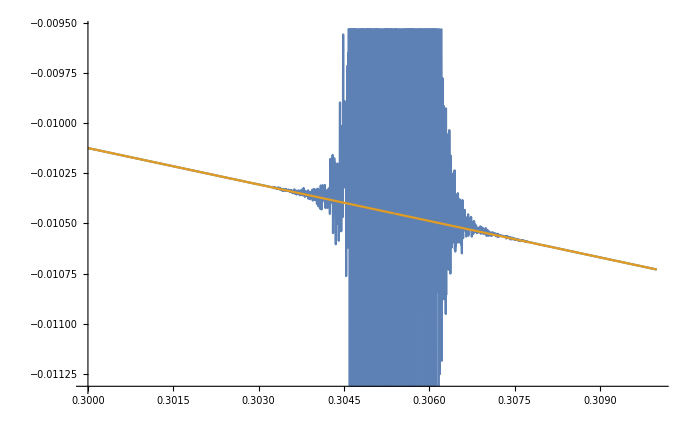

```mathematica
{test2//.kintemp2/.s23->0.0000000001,test1regular//.kintemp2}//Plot[#,{xi,0.3,0.31}]&
```

```mathematica
Plus1Bterms/.Plus1B[__,__]->1//.kintemp2/.s23->0.00000000001/.xi->0.3
//Plot[#,{xi,0.3,0.32}]&
```

-(1.69743×10^-15)/ϵ-0.0101249

$Aborted

-(5 s23^3 t^3 log((2 Q^2+s+t-√(4 s23 Q^2+(s+t)^2))/(2 Q^2+s+t+√(4 s23 Q^2+(s+t)^2))) Q^12)/(192 π^5 (s23-t)^3 (-Q^2-s+s23-t) √(4 s23 Q^2+s^2+t^2+2 s t) (4 s23 Q^2+(s+t)^2)^3)+3926+(3 s^4 s23)/(256 π^5 (s23-t) t (Q^2+(s+t)^2/(4 s23)) Q^2)
 |  |  |  |

```mathematica
test0=Plus1Bterms//Expand//Select[#,FreeQ[#,ϵ^-1 __]&]&//ReplaceAll[#,{Plus1B[_,_]->1,g->1}]&;
test1=Plus1Bterms//Expand//Select[#,FreeQ[#,ϵ^-1 __]&]&//ReplaceAll[#,{Plus1B[_,_]->1,g->1}]&//Apply[List]//Together//Apply[Plus]//ReplaceAll[#,s^2+t^2+2s t->(s+t)^2]&//Collect[#,{Log[x__]Log[x__],Log[x__]Log[y__],Log[__],PolyLog[__,__]},Simplify]&;
```

```mathematica
test1limit=test1/.s23->0//Simplify[#,s+t>0]&//ReplaceAll[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logreplace]&//Expand//Simplify
```

```mathematica
testfastlimit=test0//FastLimit//Expand//Collect[#,{Log[x__]Log[x__],Log[x__]Log[y__],Log[__],PolyLog[__,__]},Simplify]&;
testfastlimit2=test0//FastLimit;
```

Test limit: 0

Test limit: 0

```mathematica
dimcheck={log((Q^2+s-s23+t)/((s-s23) (s23-t)))->Log[(Q^2+s-s23+t)/((s-s23) (s23-t))]-2Log[dim],Log[μ]->Log[μ]+Log[dim]};
```

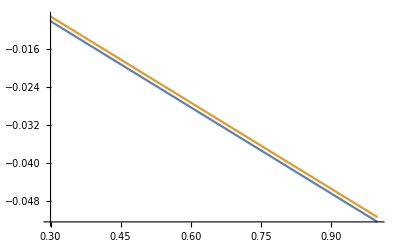

```mathematica
{(*(test0)//.kintemp2/.s23->0.0000000000001,(test1)//.kintemp2/.s23->0.0000000000001,*)(test1limit)//.kintemp2,(testfastlimit2+0.001)//.kintemp2}//Plot[#,{xi,0.3,1.0}]&
```

```mathematica
test11=test1//ReplaceRepeated[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logargreplace3]&//ReplaceRepeated[#,logreplace]&//Expand//Collect[#,{Log[__],Log4,Log4π},Simplify]&//Apply[List];
```

```mathematica
FindFactorInLimit[list_]:=Module[{i=0,den={},indices={}},
den=list//Denominator//ReplaceAll[#,s23->0]&//FullSimplify[#,s+t>0]&;
For[i=1,i≤(list//Length),i++,
If[MatchQ[den[[i]],__(s+t)^p_ ],indices=Append[indices,i],Nothing];
];
indices
]
```

```mathematica
FindFactorInLimit[test11]
```

{2,10,11}

```mathematica
(s+t+u)^3//Expand
(s+t+u)^2//Expand
```

s^3+3 s^2 t+3 s^2 u+3 s t^2+6 s t u+3 s u^2+t^3+3 t^2 u+3 t u^2+u^3

s^2+2 s t+2 s u+t^2+2 t u+u^2

```mathematica
t^6->st^6-(s+t)^6+t^6//Expand//Simplify
```

t^6→-s^6-6 s^5 t-15 s^4 t^2-20 s^3 t^3-15 s^2 t^4-6 s t^5+st^6

```mathematica
(x+x z qT^2 /(1-z)/Q^2 )//.kintemp2
kintemp2
```

0.282713

{μ2→μ^2,Log4→log(4),Log4π→log(4 π),u→-Q^2-s-t,υ→-u,τ→-t,E4Pi→ℽ-log(4 π),n_f→4,s→(Q^2 (1-xh))/xh,t→Q^2 (zh-1)-qT^2 zh,g→1,xh→x/xi,zh→(Q^2 (1-xh))/(xh ((Q^2 (1-xh))/xh+qT^2)),x→0.1326,z→0.4,Q→2.30217,qT→3,B→Q^2 (1/xh-1) (1-z)-qT^2 z,μ→Q,gp→1,δ(_)→1}

```mathematica
test11//Apply[Plus]//Expand//Apply[List]//ReplaceAll[#,t->-s]&//Apply[Plus]
```

-(3 s23^3 log(Abs[2 Q^2-2 √(Q^2 s23)]) Q^10)/(1024 π^5 s (Q^2-s23) (Q^2 s23)^(5/2))+(3 s23^3 log(Abs[2 Q^2+2 √(Q^2 s23)]) Q^10)/(1024 π^5 s (Q^2-s23) (Q^2 s23)^(5/2))-(63 s23^3 log(Abs[2 Q^2-2 √(Q^2 s23)]) Q^8)/(4096 π^5 (Q^2-s23) (Q^2 s23)^(5/2))+(5 s s23^2 log(Abs[2 Q^2-2 √(Q^2 s23)]) Q^8)/(1536 π^5 (Q^2-s23) (Q^2 s23)^(5/2))+(63 s23^3 log(Abs[2 Q^2+2 √(Q^2 s23)]) Q^8)/(4096 π^5 (Q^2-s23) (Q^2 s23)^(5/2))-(5 s s23^2 log(Abs[2 Q^2+2 √(Q^2 s23)]) Q^8)/(1536 π^5 (Q^2-s23) (Q^2 s23)^(5/2))+(3 s23^7 log(Abs[μ]) Q^8)/(32 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(3 s23^6 log(Abs[μ]) Q^8)/(32 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(13 s23^5 log(Abs[μ]) Q^8)/(96 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(5 s s23^4 log(Abs[μ]) Q^8)/(24 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(s^2 s23^3 log(Abs[μ]) Q^8)/(96 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(5 s^3 s23^2 log(Abs[μ]) Q^8)/(32 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(3 Log4π s23^7 Q^8)/(64 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(3 ℽ s23^7 Q^8)/(64 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(3 Log4π s23^6 Q^8)/(64 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(3 ℽ s23^6 Q^8)/(64 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(19 s23^6 Q^8)/(192 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(23 Log4π s23^5 Q^8)/(192 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(23 ℽ s23^5 Q^8)/(192 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(17 s23^5 Q^8)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(Log4π s s23^4 Q^8)/(12 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(ℽ s s23^4 Q^8)/(12 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(51 s s23^4 Q^8)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(19 Log4π s^2 s23^3 Q^8)/(192 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(19 ℽ s^2 s23^3 Q^8)/(192 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(27 s^2 s23^3 Q^8)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(Log4π s^3 s23^2 Q^8)/(64 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(ℽ s^3 s23^2 Q^8)/(64 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(37 s^3 s23^2 Q^8)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(3 s23^2 log(Abs[Q]) Q^6)/(32 π^5 s^2 (Q^2-s23)^2)+(3 s23 log(Abs[Q]) Q^6)/(32 π^5 s (Q^2-s23)^2)-(3 s23^3 log(Abs[Q^2-s23]) Q^6)/(64 π^5 s^2 (Q^2-s23)^2 (s+s23))-(3 s23^2 log(Abs[Q^2-s23]) Q^6)/(32 π^5 s (Q^2-s23)^2 (s+s23))-(9 s23 log(Abs[Q^2-s23]) Q^6)/(128 π^5 (Q^2-s23)^2 (s+s23))+(3 s23^4 log(Abs[s+s23]) Q^6)/(32 π^5 s^2 (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(3 s23^3 log(Abs[s+s23]) Q^6)/(16 π^5 s (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(15 s23^2 log(Abs[s+s23]) Q^6)/(128 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(9 s23^4 log(Abs[2 Q^2-2 √(Q^2 s23)]) Q^6)/(2048 π^5 (Q^2-s23) (Q^2 s23)^(5/2))+(5 s s23^3 log(Abs[2 Q^2-2 √(Q^2 s23)]) Q^6)/(1536 π^5 (Q^2-s23) (Q^2 s23)^(5/2))-(37 s^2 s23^2 log(Abs[2 Q^2-2 √(Q^2 s23)]) Q^6)/(12288 π^5 (Q^2-s23) (Q^2 s23)^(5/2))-(9 s23^4 log(Abs[2 Q^2+2 √(Q^2 s23)]) Q^6)/(2048 π^5 (Q^2-s23) (Q^2 s23)^(5/2))-(5 s s23^3 log(Abs[2 Q^2+2 √(Q^2 s23)]) Q^6)/(1536 π^5 (Q^2-s23) (Q^2 s23)^(5/2))+(37 s^2 s23^2 log(Abs[2 Q^2+2 √(Q^2 s23)]) Q^6)/(12288 π^5 (Q^2-s23) (Q^2 s23)^(5/2))-(15 s23^8 log(Abs[μ]) Q^6)/(32 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(21 s23^7 log(Abs[μ]) Q^6)/(32 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(89 s23^6 log(Abs[μ]) Q^6)/(192 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(47 s s23^5 log(Abs[μ]) Q^6)/(48 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(395 s^2 s23^4 log(Abs[μ]) Q^6)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(23 s^3 s23^3 log(Abs[μ]) Q^6)/(128 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(137 s^4 s23^2 log(Abs[μ]) Q^6)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(83 s^5 s23 log(Abs[μ]) Q^6)/(192 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(3 Log4π s23^8 Q^6)/(64 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(3 ℽ s23^8 Q^6)/(64 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(9 s23^8 Q^6)/(32 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(9 Log4π s23^7 Q^6)/(64 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(9 ℽ s23^7 Q^6)/(64 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(3 Log4π s23^6 Q^6)/(128 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(3 ℽ s23^6 Q^6)/(128 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(1109 s23^6 Q^6)/(2048 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(31 Log4π s s23^5 Q^6)/(96 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(31 ℽ s s23^5 Q^6)/(96 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(3 s s23^5 Q^6)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(139 Log4π s^2 s23^4 Q^6)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(139 ℽ s^2 s23^4 Q^6)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(9 s^2 s23^4 Q^6)/(1024 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(87 Log4π s^3 s23^3 Q^6)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(87 ℽ s^3 s23^3 Q^6)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(41 s^3 s23^3 Q^6)/(96 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(151 Log4π s^4 s23^2 Q^6)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(151 ℽ s^4 s23^2 Q^6)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(1475 s^4 s23^2 Q^6)/(6144 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(5 Log4π s^5 s23 Q^6)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(5 ℽ s^5 s23 Q^6)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(s^5 s23 Q^6)/(48 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(15 s23^3 log(Abs[Q]) Q^4)/(32 π^5 s^2 (Q^2-s23)^2)-(21 s23^2 log(Abs[Q]) Q^4)/(32 π^5 s (Q^2-s23)^2)-(3 s23 log(Abs[Q]) Q^4)/(16 π^5 (Q^2-s23)^2)-(17 s log(Abs[Q]) Q^4)/(384 π^5 (Q^2-s23)^2)-(3 s23^2 log(Abs[s]) Q^4)/(32 π^5 s^2 (Q^2-s23))-(3 s23 log(Abs[s]) Q^4)/(32 π^5 s (Q^2-s23))-(s log(Abs[s]) Q^4)/(384 π^5 (Q^2-s23)^2)+(15 s23^4 log(Abs[Q^2-s23]) Q^4)/(64 π^5 s^2 (Q^2-s23)^2 (s+s23))+(9 s23^3 log(Abs[Q^2-s23]) Q^4)/(16 π^5 s (Q^2-s23)^2 (s+s23))+(33 s23^2 log(Abs[Q^2-s23]) Q^4)/(64 π^5 (Q^2-s23)^2 (s+s23))+(179 s s23 log(Abs[Q^2-s23]) Q^4)/(768 π^5 (Q^2-s23)^2 (s+s23))+(89 s^2 log(Abs[Q^2-s23]) Q^4)/(768 π^5 (Q^2-s23)^2 (s+s23))-(s^3 log(Abs[s-s23]) Q^4)/(384 π^5 (Q^2-s23)^2 (Q^2 s23-s^2))+(s log(Abs[s-s23]) Q^4)/(384 π^5 (Q^2-s23)^2)-(3 s23^5 log(Abs[s+s23]) Q^4)/(8 π^5 s^2 (Q^2-s23) (s+s23) (Q^2 s23-s^2))-(15 s23^4 log(Abs[s+s23]) Q^4)/(16 π^5 s (Q^2-s23) (s+s23) (Q^2 s23-s^2))-(117 s23^3 log(Abs[s+s23]) Q^4)/(128 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))-(69 s s23^2 log(Abs[s+s23]) Q^4)/(128 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))-(33 s^2 s23 log(Abs[s+s23]) Q^4)/(128 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))-(15 s23^5 log(Abs[2 Q^2-2 √(Q^2 s23)]) Q^4)/(4096 π^5 (Q^2-s23) (Q^2 s23)^(5/2))-(15 s^2 s23^3 log(Abs[2 Q^2-2 √(Q^2 s23)]) Q^4)/(2048 π^5 (Q^2-s23) (Q^2 s23)^(5/2))+(15 s23^5 log(Abs[2 Q^2+2 √(Q^2 s23)]) Q^4)/(4096 π^5 (Q^2-s23) (Q^2 s23)^(5/2))+(15 s^2 s23^3 log(Abs[2 Q^2+2 √(Q^2 s23)]) Q^4)/(2048 π^5 (Q^2-s23) (Q^2 s23)^(5/2))+(21 s23^9 log(Abs[μ]) Q^4)/(32 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(33 s23^8 log(Abs[μ]) Q^4)/(32 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(15 s23^7 log(Abs[μ]) Q^4)/(64 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(241 s s23^6 log(Abs[μ]) Q^4)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(329 s^2 s23^5 log(Abs[μ]) Q^4)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(485 s^3 s23^4 log(Abs[μ]) Q^4)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(s^4 s23^3 log(Abs[μ]) Q^4)/(192 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(341 s^5 s23^2 log(Abs[μ]) Q^4)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(145 s^6 s23 log(Abs[μ]) Q^4)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(13 s^7 log(Abs[μ]) Q^4)/(48 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(15 Log4π s23^9 Q^4)/(64 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(15 ℽ s23^9 Q^4)/(64 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(9 s23^9 Q^4)/(16 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(27 Log4π s23^8 Q^4)/(64 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(27 ℽ s23^8 Q^4)/(64 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(55 s23^8 Q^4)/(192 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(101 Log4π s23^7 Q^4)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(101 ℽ s23^7 Q^4)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(1331 s23^7 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(1075 Log4π s s23^6 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(1075 ℽ s s23^6 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(707 s s23^6 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(155 Log4π s^2 s23^5 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(155 ℽ s^2 s23^5 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(89 s^2 s23^5 Q^4)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(539 Log4π s^3 s23^4 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(539 ℽ s^3 s23^4 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(1111 s^3 s23^4 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(27 Log4π s^4 s23^3 Q^4)/(128 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(27 ℽ s^4 s23^3 Q^4)/(128 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(535 s^4 s23^3 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(181 Log4π s^5 s23^2 Q^4)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(181 ℽ s^5 s23^2 Q^4)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(19 s^5 s23^2 Q^4)/(64 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(Log4π s^6 s23 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(ℽ s^6 s23 Q^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(55 s^6 s23 Q^4)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(19 s^7 Q^4)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(21 s23^4 log(Abs[Q]) Q^2)/(32 π^5 s^2 (Q^2-s23)^2)+(33 s23^3 log(Abs[Q]) Q^2)/(32 π^5 s (Q^2-s23)^2)+(3 s23^2 log(Abs[Q]) Q^2)/(8 π^5 (Q^2-s23)^2)+(3 s s23 log(Abs[Q]) Q^2)/(64 π^5 (Q^2-s23)^2)+(3 s23^3 log(Abs[s]) Q^2)/(8 π^5 s^2 (Q^2-s23))+(9 s23^2 log(Abs[s]) Q^2)/(16 π^5 s (Q^2-s23))+(3 s23 log(Abs[s]) Q^2)/(16 π^5 (Q^2-s23))+(3 s log(Abs[s]) Q^2)/(64 π^5 (Q^2-s23))-(21 s23^5 log(Abs[Q^2-s23]) Q^2)/(64 π^5 s^2 (Q^2-s23)^2 (s+s23))-(27 s23^4 log(Abs[Q^2-s23]) Q^2)/(32 π^5 s (Q^2-s23)^2 (s+s23))-(105 s23^3 log(Abs[Q^2-s23]) Q^2)/(128 π^5 (Q^2-s23)^2 (s+s23))-(57 s s23^2 log(Abs[Q^2-s23]) Q^2)/(128 π^5 (Q^2-s23)^2 (s+s23))-(27 s^2 s23 log(Abs[Q^2-s23]) Q^2)/(128 π^5 (Q^2-s23)^2 (s+s23))+(3 s23 log(Abs[s-s23]) Q^2)/(128 π^5 (s+s23))+(s^3 s23 log(Abs[s-s23]) Q^2)/(384 π^5 (Q^2-s23)^2 (Q^2 s23-s^2))+(s^4 log(Abs[s-s23]) Q^2)/(384 π^5 (Q^2-s23)^2 (Q^2 s23-s^2))+(9 s23^6 log(Abs[s+s23]) Q^2)/(32 π^5 s^2 (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(3 s23^5 log(Abs[s+s23]) Q^2)/(4 π^5 s (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(69 s23^4 log(Abs[s+s23]) Q^2)/(64 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(159 s s23^3 log(Abs[s+s23]) Q^2)/(128 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(117 s^2 s23^2 log(Abs[s+s23]) Q^2)/(128 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(67 s^3 s23 log(Abs[s+s23]) Q^2)/(192 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(53 s^4 log(Abs[s+s23]) Q^2)/(384 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(s^3 log(Abs[Q^2 s23-s^2]) Q^2)/(384 π^5 (Q^2-s23) (Q^2 s23-s^2))+(9 s^2 s23^4 log(Abs[2 Q^2-2 √(Q^2 s23)]) Q^2)/(4096 π^5 (Q^2-s23) (Q^2 s23)^(5/2))-(9 s^2 s23^4 log(Abs[2 Q^2+2 √(Q^2 s23)]) Q^2)/(4096 π^5 (Q^2-s23) (Q^2 s23)^(5/2))-(9 s23^10 log(Abs[μ]) Q^2)/(32 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(15 s23^9 log(Abs[μ]) Q^2)/(32 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(3 s23^8 log(Abs[μ]) Q^2)/(8 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(227 s s23^7 log(Abs[μ]) Q^2)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(17 s^2 s23^6 log(Abs[μ]) Q^2)/(16 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(177 s^3 s23^5 log(Abs[μ]) Q^2)/(128 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(139 s^4 s23^4 log(Abs[μ]) Q^2)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(171 s^5 s23^3 log(Abs[μ]) Q^2)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(287 s^6 s23^2 log(Abs[μ]) Q^2)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(31 s^7 s23 log(Abs[μ]) Q^2)/(64 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(9 Log4π s23^10 Q^2)/(64 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(9 ℽ s23^10 Q^2)/(64 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(9 s23^10 Q^2)/(32 π^5 s^2 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(15 Log4π s23^9 Q^2)/(64 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(15 ℽ s23^9 Q^2)/(64 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(3 s23^9 Q^2)/(16 π^5 s (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(Log4π s23^8 Q^2)/(48 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(ℽ s23^8 Q^2)/(48 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(47 s23^8 Q^2)/(2048 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(31 Log4π s s23^7 Q^2)/(512 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(31 ℽ s s23^7 Q^2)/(512 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(97 s s23^7 Q^2)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(31 Log4π s^2 s23^6 Q^2)/(96 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(31 ℽ s^2 s23^6 Q^2)/(96 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(2755 s^2 s23^6 Q^2)/(3072 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(371 Log4π s^3 s23^5 Q^2)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(371 ℽ s^3 s23^5 Q^2)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(25 s^3 s23^5 Q^2)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(193 Log4π s^4 s23^4 Q^2)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(193 ℽ s^4 s23^4 Q^2)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(313 s^4 s23^4 Q^2)/(3072 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(929 Log4π s^5 s23^3 Q^2)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(929 ℽ s^5 s23^3 Q^2)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(1043 s^5 s23^3 Q^2)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(Log4π s^6 s23^2 Q^2)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(ℽ s^6 s23^2 Q^2)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(977 s^6 s23^2 Q^2)/(3072 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(11 Log4π s^7 s23 Q^2)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(11 ℽ s^7 s23 Q^2)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(47 s^7 s23 Q^2)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(37 s^8 Q^2)/(6144 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(9 s23^5 log(Abs[Q]))/(32 π^5 s^2 (Q^2-s23)^2)-(15 s23^4 log(Abs[Q]))/(32 π^5 s (Q^2-s23)^2)-(3 s23^3 log(Abs[Q]))/(16 π^5 (Q^2-s23)^2)-(9 s23^4 log(Abs[s]))/(32 π^5 s^2 (Q^2-s23))-(15 s23^3 log(Abs[s]))/(32 π^5 s (Q^2-s23))-(3 s23^2 log(Abs[s]))/(16 π^5 (Q^2-s23))+(9 s23^6 log(Abs[Q^2-s23]))/(64 π^5 s^2 (Q^2-s23)^2 (s+s23))+(3 s23^5 log(Abs[Q^2-s23]))/(8 π^5 s (Q^2-s23)^2 (s+s23))+(3 s23^4 log(Abs[Q^2-s23]))/(8 π^5 (Q^2-s23)^2 (s+s23))+(27 s s23^3 log(Abs[Q^2-s23]))/(128 π^5 (Q^2-s23)^2 (s+s23))+(3 s^2 s23^2 log(Abs[Q^2-s23]))/(32 π^5 (Q^2-s23)^2 (s+s23))-(3 s^2 log(Abs[s-s23]))/(32 π^5 (s+s23))-(3 s23^2 log(Abs[s-s23]))/(64 π^5 (s+s23))-(15 s s23 log(Abs[s-s23]))/(128 π^5 (s+s23))-(s^4 s23 log(Abs[s-s23]))/(384 π^5 (Q^2-s23)^2 (Q^2 s23-s^2))-(s^4 log(Abs[s-s23]))/(384 π^5 (Q^2-s23) (Q^2 s23-s^2))-(9 s23^5 log(Abs[s+s23]))/(32 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))-(3 s s23^4 log(Abs[s+s23]))/(4 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))-(45 s^2 s23^3 log(Abs[s+s23]))/(64 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))-(39 s^3 s23^2 log(Abs[s+s23]))/(128 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))-(3 s^4 s23 log(Abs[s+s23]))/(32 π^5 (Q^2-s23) (s+s23) (Q^2 s23-s^2))+(9 s23^9 log(Abs[μ]))/(32 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(15 s s23^8 log(Abs[μ]))/(32 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(9 s^2 s23^7 log(Abs[μ]))/(32 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(565 s^3 s23^6 log(Abs[μ]))/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(23 s^4 s23^5 log(Abs[μ]))/(64 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(169 s^5 s23^4 log(Abs[μ]))/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(71 s^6 s23^3 log(Abs[μ]))/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(27 s^7 s23^2 log(Abs[μ]))/(128 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(9 Log4π s23^9)/(64 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(9 ℽ s23^9)/(64 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(9 s23^9)/(32 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(15 Log4π s s23^8)/(64 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(15 ℽ s s23^8)/(64 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(3 s s23^8)/(16 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(41 Log4π s^2 s23^7)/(192 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(41 ℽ s^2 s23^7)/(192 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(293 s^2 s23^7)/(512 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(247 Log4π s^3 s23^6)/(512 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(247 ℽ s^3 s23^6)/(512 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(179 s^3 s23^6)/(512 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(5 Log4π s^4 s23^5)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(5 ℽ s^4 s23^5)/(384 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(349 s^4 s23^5)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(553 Log4π s^5 s23^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(553 ℽ s^5 s23^4)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(187 s^5 s23^4)/(512 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(Log4π s^6 s23^3)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(ℽ s^6 s23^3)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(311 s^6 s23^3)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(23 Log4π s^7 s23^2)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(23 ℽ s^7 s23^2)/(768 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(9 s^7 s23^2)/(256 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))+(11 s^8 s23)/(1536 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2))-(27 s^4 s23^6)/(2048 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2) Q^2)+(27 s^6 s23^4)/(1024 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2) Q^2)-(27 s^8 s23^2)/(2048 π^5 (Q^2-s23)^2 (s-s23)^2 (s+s23)^2 (Q^2 s23-s^2) Q^2)

```mathematica
test11[[10]]+test11[[11]]//Series[#,{s23,0,1}]&//Normal//Expand//Simplify
test11[[2]]//Series[#,{s23,0,1}]&//Normal//Expand//Simplify
```

1/(1536 π^5 t (s+t)^3 √((s+t)^2) (Q^2+s+t))(2 Q^6 s23 (-27 s^3+32 s^2 t+29 s t^2+18 t^3)+2 Q^4 s23 (-45 s^4-40 s^3 t+27 s^2 t^2+31 s t^3+9 t^4)+Q^2 (s+t)^2 (s^3 (34 t-36 s23)+s^2 (68 t^2-38 s23 t)+s t^2 (34 t-5 s23)-9 s23 t^3)+t (s+t)^3 (34 s^3+34 s^2 (s23+2 t)+34 s t (s23+t)-9 s23 t^2)) log(Abs[2 Q^2+s+t-√(4 s23 Q^2+(s+t)^2)]/Abs[2 Q^2+s+t+√(4 s23 Q^2+(s+t)^2)])

1/(1536 π^5 Q^2 t (s+t)^3 (Q^2+s+t))(Q^6 s23 ((7-20 ℽ) s^3+(247-60 ℽ) s^2 t+(241-60 ℽ) s t^2+(97-20 ℽ) t^3)+Q^4 (s+t) (2 s^3 ((106 ℽ-89) s23-24 t)+s^2 t ((637 ℽ-41) s23-96 t)+2 s t^2 ((127+319 ℽ) s23-24 t)+(143+213 ℽ) s23 t^3)+Q^2 (s+t)^2 (s^3 ((232 ℽ-113) s23-48 t)+3 s^2 t ((14+253 ℽ) s23-32 t)+s t^2 ((403+778 ℽ) s23-48 t)+(237+251 ℽ) s23 t^3)+72 s23 (s+t)^5 (s+3 t))

```mathematica
1/(1536 π^5 t (s+t)^3 √((s+t)^2) (Q^2+s+t))(2 Q^6 s23 (-27 s^3+32 s^2 t+29 s t^2+18 t^3)+2 Q^4 s23 (-45 s^4-40 s^3 t+27 s^2 t^2+31 s t^3+9 t^4)+Q^2 (s+t)^2 (s^3 (34 t-36 s23)+s^2 (68 t^2-38 s23 t)+s t^2 (34 t-5 s23)-9 s23 t^3)+t (s+t)^3 (34 s^3+34 s^2 (s23+2 t)+34 s t (s23+t)-9 s23 t^2)) log(Abs[2 Q^2+s+t-√(4 s23 Q^2+(s+t)^2)]/Abs[2 Q^2+s+t+√(4 s23 Q^2+(s+t)^2)])
```

```mathematica
1/(1536 π^5 t (s+t)^3 √((s+t)^2) (Q^2))(2 Q^6 s23 (-27 s^3-32 s^2 s+29 s s^2-18 s^3)+2 Q^4 s23 (-45 s^4+40 s^3 s+27 s^2 s^2-31 s s^3+9 s^4)+Q^2 (s+t)^2 (s^3 (-34 s-36 s23)+s^2 (68 s^2+38 s23 s)+s s^2 (-34 s-5 s23)+9 s23 s^3)-s (s+t)^3 (34 s^3+34 s^2 (s23-2 s)-34 s s (s23-s)-9 s23 s^2)) log(Abs[2 Q^2-√(4 s23 Q^2)]/Abs[2 Q^2+√(4 s23 Q^2)])//Simplify
```

(s^3 s23 (-32 Q^6+2 Q^2 (s+t)^2+3 (s+t)^3) log(Abs[2 Q^2-2 √(Q^2 s23)]/(2 Abs[Q^2+√(Q^2 s23)])))/(512 π^5 Q^2 t (s+t)^3 √((s+t)^2))

```mathematica
kintemp2
```

{μ2→μ^2,Log4→log(4),Log4π→log(4 π),u→-Q^2-s-t,υ→-u,τ→-t,E4Pi→ℽ-log(4 π),n_f→4,s→(Q^2 (1-xh))/xh,t→Q^2 (zh-1)-qT^2 zh,g→1,xh→x/xi,zh→(Q^2 (1-xh))/(xh ((Q^2 (1-xh))/xh+qT^2)),x→0.1326,z→0.4,Q→2.30217,qT→3,B→Q^2 (1/xh-1) (1-z)-qT^2 z,μ→Q,gp→1,δ(_)→1}

```mathematica
num1=test11[[10]]/.Log[__]->1//Numerator//Expand//Collect[#,s23,Simplify]&//Apply[List]//ReplaceAll[#,s+t->st]&;

//ReplaceAll[#,t^6->(st^6-(s+t)^6+t^6//Expand//Simplify)]&
```

```mathematica
maldestamreplace={s+t+u->stu,s+t+u+x__->stu+x,a_ s+ a_ u + x__->a stu - a t +x};
test11[[10]]/.Log[__]->1//Numerator//Expand//PolynomialReduce[#,{(s+t)^5,(s+t)^4,(s+t)^3,(s+t)^2,(s+t)},{s,t}]&(*//ReplaceRepeated[#,Q^p_->(s23-u-t-s)^(p/2)]&*)//Expand//Collect[#,{s23},FullSimplify]&//ReplaceRepeated[#,maldestamreplace]&
```

{{s23^2 (82 Q^2+7 s+13 t)-2 Q^2 s23 (45 Q^2+18 s-187 t)+34 s t (Q^2+s+t),s23^3 (28 Q^2-18 t)+s23^2 (115 Q^4-221 Q^2 t-51 t^2)+s23 (-54 Q^6+620 Q^4 t-377 Q^2 t^2-9 t^3),2 s23^3 (68 Q^4+6 Q^2 t+27 t^2)+2 Q^2 s23 t (113 Q^4-293 Q^2 t-3 t^2)+s23^2 (-60 Q^6+274 Q^4 t-92 Q^2 t^2+38 t^3),s23 (74 Q^4 t^3-232 Q^6 t^2)+s23^4 (96 Q^4-36 Q^2 t)+s23^3 (460 Q^6-356 Q^4 t+252 Q^2 t^2-54 t^3)+s23^2 (-84 Q^8+868 Q^6 t-500 Q^4 t^2+168 Q^2 t^3),96 Q^6 s23 t^3+12 Q^2 s23^4 t (10 Q^2-9 t)+4 Q^4 s23^2 t (106 Q^4-147 Q^2 t+12 t^2)+8 s23^3 (54 Q^8-132 Q^6 t+5 Q^4 t^2-50 Q^2 t^3)},-180 Q^4 s23^5 t-4 Q^6 s23^2 t^2 (40 Q^2+37 t)+108 Q^2 s23^4 t (2 Q^4+t^2)+4 Q^4 s23^3 (36 Q^6-189 Q^4 t-40 Q^2 t^2-90 t^3)}

```mathematica
test11[[10]]/.Log[__]->1//Numerator//PolynomialReduce[#,{s+t},{s,t}]&
```

```mathematica
(36 s^3+27 s^2 (11 t+4 u)+2 s (223 t^2+297 t u+54 u^2)+275 t^3+446 t^2 u+297 t u^2+36 u^3)
```

{{432 Q^8 s23^3+s^5 (7 s23^2-36 Q^2 s23)+34 Q^2 s^5 t+s^4 t (230 Q^2 s23+41 s23^2)+136 Q^2 s^4 t^2+s^3 t^2 (903 Q^2 s23+43 s23^2)+s^3 t^3 (204 Q^2-9 s23)+s^2 t^3 (963 Q^2 s23-9 s23^2)+s^2 t^4 (136 Q^2-27 s23)+s t^4 (317 Q^2 s23-18 s23^2)+s t^5 (34 Q^2-27 s23)-9 Q^2 s23 t^5+s^2 (136 Q^4 s23^3-60 Q^6 s23^2)+s^4 (82 Q^2 s23^2-90 Q^4 s23)+s^3 t (260 Q^4 s23+107 Q^2 s23^2-18 s23^3)+s^2 t^2 (734 Q^4 s23-263 Q^2 s23^2)+s t^3 (402 Q^4 s23-351 Q^2 s23^2)+t^4 (18 Q^4 s23-63 Q^2 s23^2-18 s23^3)+s (-84 Q^8 s23^2+460 Q^6 s23^3+96 Q^4 s23^4)+t (340 Q^8 s23^2-596 Q^6 s23^3+216 Q^4 s23^4)+s^3 (-54 Q^6 s23+115 Q^4 s23^2+28 Q^2 s23^3)+s^2 t (64 Q^6 s23+619 Q^4 s23^2+96 Q^2 s23^3)+s t^2 (58 Q^6 s23+393 Q^4 s23^2+360 Q^2 s23^3)+s t (748 Q^6 s23^2-84 Q^4 s23^3-36 Q^2 s23^4)+t^3 (36 Q^6 s23-63 Q^4 s23^2-108 Q^2 s23^3)+t^2 (220 Q^6 s23^2-180 Q^4 s23^3-144 Q^2 s23^4)+34 s^6 t+170 s^5 t^2+340 s^4 t^3+340 s^3 t^4+170 s^2 t^5+34 s t^6-9 s23 t^6},144 Q^10 s23^3+t^2 (-160 Q^8 s23^2-160 Q^6 s23^3)+t (-756 Q^8 s23^3+216 Q^6 s23^4-180 Q^4 s23^5)+t^3 (-148 Q^6 s23^2-360 Q^4 s23^3+108 Q^2 s23^4)}

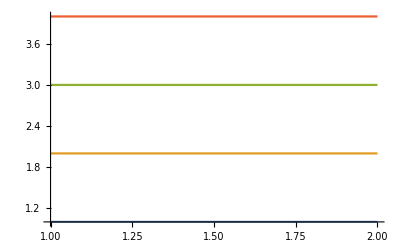

```mathematica
Plot[{1,2,3,4},{x,1,2}]
```

```mathematica
kintemp2
```

{μ2→μ^2,Log4→log(4),Log4π→log(4 π),u→-Q^2-s-t,υ→-u,τ→-t,E4Pi→ℽ-log(4 π),n_f→4,s→(Q^2 (1-xh))/xh,t→Q^2 (zh-1)-qT^2 zh,g→1,xh→x/xi,zh→(Q^2 (1-xh))/(xh ((Q^2 (1-xh))/xh+qT^2)),x→0.1326,z→0.4,Q→2.30217,qT→3,B→Q^2 (1/xh-1) (1-z)-qT^2 z,μ→Q,s23→1.×10^-10,gp→1,δ(_)→1}

```mathematica
plotpieces={list21,list31,list41,list51}//.kintemp3;
```

$Aborted

$Aborted

1.38629 f(0.5) ϵ+2. f(0.5)

```mathematica
(ϵ log(1-z))/(z-1)//Limit[#,z->1]&
```

ϵ (-∞)

```mathematica
kintemp3={μ2->μ^2,Log4->log(4),Log4π->log(4 π),u->-Q^2-s-t,υ->-u,τ->-t,E4Pi->ℽ-log(4 π),Subscript[n, f]->4,s->(Q^2 (1-xh))/xh,t->Q^2 (zh-1)-qT^2 zh,g->1,xh->x/xi,zh->(Q^2 (1-xh))/(xh ((Q^2 (1-xh))/xh+qT^2)),x->0.1326,z->0.4,Q->2.3021728866442674,qT->3,B->Q^2 (1/xh-1) (1-z)-qT^2 z,μ->Q,gp->1,δ(_)->1};
```

```mathematica
deltaterms//.kintemp3/.xi->0.4
```

$Aborted

```mathematica
varreplace
logargreplace1
logargreplace2
logargreplace3
logreplace
polylogargreplace
```

{Q^p_→(-s+τ+υ)^(p/2),t→-τ,u→-υ,μ^2→μ2,log(μ)→(log(μ2))/2,ℽ→E4Pi+log(4 π)}

{log(x_):>log(Abs[Simplify[Factor[x]]])}

{log(Abs[x_ y_])→log(Abs[x])+log(Abs[y]),log(1/x_)→-log(x)}

{log(Abs[x_]):>log(√Abs[Simplify[x^2]])}

{log(a_/b_)→log(a)-log(b),log(a_ b_^p_)→log(a)+p log(b),log(a_^p_)→p log(a),log(n_Integer x__)→log(n)+log(x),log(x__ Rational[a_,b_])→log(a)-log(b)+log(x),log(π n_Integer)→-Log4+Log4π+log(n),log(n_Integer):>Log4 log_4(n),log(π)→Log4π-Log4}

{n_x_:>nSimplify[Factor[x]]}

```mathematica
varreplace
```

{Q^p_→(-s-t-u)^(p/2),μ^2→μ2,log(μ)→(log(μ2))/2,ℽ→E4Pi+log(4 π)}

```mathematica
deltatermss230//Select[#,FreeQ[#,ϵ^-1__]&&FreeQ[#,ϵ^-2__]&]&//ReplaceAll[#,{δ[0]->1,g->1}]&//Collect[#,Log[__],Simplify]&//ReplaceRepeated[#,varreplace]&//ReplaceRepeated[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logargreplace3]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,polylogargreplace]&//ReplaceRepeated[#,varreplace]&//Expand//Select[#,MatchQ[#,Log[__]__]&&FreeQ[#,Log[x__]Log[x__]__]&&FreeQ[#,Log[x__]Log[y__]__]&]&//Apply[List]//Cases[#,Log[x__]__->Log[x]]&//DeleteDuplicates;
```

```mathematica
list1=deltatermss230//Expand//Select[#,FreeQ[#,ϵ^-1__]&&FreeQ[#,ϵ^-2__]&]&//ReplaceAll[#,{δ[0]->1,g->1}]&//Select[#,MatchQ[#,Log[__]__]&&FreeQ[#,Log[x__]Log[x__]__]&&FreeQ[#,Log[x__]Log[y__]__]&]&//Apply[List]//Cases[#,Log[x__]__->Log[x]]&//DeleteDuplicates;
list2=deltatermss230//Expand//Select[#,FreeQ[#,ϵ^-1__]&&FreeQ[#,ϵ^-2__]&]&//ReplaceAll[#,{δ[0]->1,g->1}]&//Select[#,MatchQ[#,Log[x__]Log[x__]__]&]&//Apply[List]//Cases[#,Log[x__]Log[x__]__->Log[x]Log[x]]&//DeleteDuplicates;
list3=deltatermss230//Expand//Select[#,FreeQ[#,ϵ^-1__]&&FreeQ[#,ϵ^-2__]&]&//ReplaceAll[#,{δ[0]->1,g->1}]&//Select[#,MatchQ[#,Log[x__]Log[y__]__]&]&//Apply[List]//Cases[#,Log[x__]Log[y__]__->Log[x]Log[y]]&//DeleteDuplicates;
```

```mathematica
list1//ReplaceRepeated[#,varreplace]&//ReplaceRepeated[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logargreplace3]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,polylogargreplace]&//ReplaceRepeated[#,varreplace]&
list2//ReplaceRepeated[#,varreplace]&//ReplaceRepeated[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logargreplace3]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,polylogargreplace]&//ReplaceRepeated[#,varreplace]&
list3//ReplaceRepeated[#,varreplace]&//ReplaceRepeated[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logargreplace3]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,polylogargreplace]&//ReplaceRepeated[#,varreplace]&//Part[#,-13]&
```

```mathematica
(*s+t//.kintemp2//Plot[#,{xi,0.3,0.32}]&
*)
temp1[ηval_]=list3[[-13]]//.{t->-s*η,s->2Q^2,Q->2,η->ηval}/.Log[x_]:>Log[Simplify[x]];
temp2[ηval_]:=temp1[η]//Limit[#,η->ηval]&;
(*//Plot[#,{η,0,2}]&*)

(*//.kintemp2//Plot[#,{xi,0.3,1.0}]&
*)
```

```mathematica
s+t//.{t->-s*η,s->2Q^2,Q->2,η->ηval}
```

8-8 ηval

```mathematica
temp3[ηval_]:=list3[[-13]]/.Log[x_]:>Log[Simplify[x]]/.Log[x_]Log[y_]->1/4(Log[x y]^2-Log[x/y]^2)//.{t->-s*η,s->2Q^2,Q->2,η->ηval}
```

```mathematica
temp1[η]
```

log((3-2 η)/(-η+√((η-1)^2)+2)) log((η+√((η-1)^2)-1)/(√((η-1)^2)))

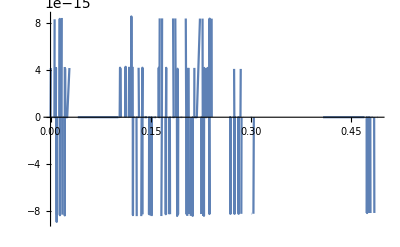

((log(Abs[s+t+2 u+√((s+t)^2)])-log(Abs[s+t+2 u-√((s+t)^2)]))^2 s^9)/(1536 π^5 (s^2+2 t s+t^2)^(7/2) u)+(log(Abs[B]) (log(Abs[s+t+2 u+√((s+t)^2)])-log(Abs[s+t+2 u-√((s+t)^2)])) s^9)/(768 π^5 (s^2+2 t s+t^2)^(7/2) u)-(Log4 (log(Abs[s+t+2 u+√((s+t)^2)])-log(Abs[s+t+2 u-√((s+t)^2)])) s^9)/(768 π^5 (s^2+2 t s+t^2)^(7/2) u)+2763+(5 (E4Pi+Log4π) t^8)/(6144 π^5 (s^2+2 t s+t^2)^3 u)-(5 (Log4π-Log4) t^8)/(6144 π^5 (s^2+2 t s+t^2)^3 u)-(3 t^8)/(1024 π^5 (s^2+2 t s+t^2)^3 u)
 |  |  |  |

```mathematica
Plot[temp1[η],{η,0,1},PlotRange->All]
```

### separate terms : log, double log, polylog, rational

```mathematica
all=deltatermss230//Select[#,FreeQ[#,ϵ^-1__]&&FreeQ[#,ϵ^-2__]&]&//ReplaceAll[#,{δ[0]->1,g->1}]&//Collect[#,Log[__],Simplify]&//ReplaceRepeated[#,varreplace]&//ReplaceRepeated[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logargreplace3]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,polylogargreplace]&//ReplaceRepeated[#,varreplace]&//Expand;

log=all//Select[#,MatchQ[#,Log[__]__]&&FreeQ[#,Log[x__]Log[x__]__]&&FreeQ[#,Log[x__]Log[y__]__]&]&;

doublelog=all//Select[#,MatchQ[#,Log[x__]Log[x__]__]||MatchQ[#,Log[x__]Log[y__]__]&]&;

polylog=all//Select[#,MatchQ[#,PolyLog[__,__]__]&]&;

rational=all//Select[#,FreeQ[#,Log[x__]__]&&FreeQ[#,Log[x__]Log[x__]__]&&FreeQ[#,Log[x__]Log[y__]__]&&FreeQ[#,PolyLog[__,__]__]&]&;

(all//Length)-(log//Length)-(doublelog//Length)-(polylog//Length)-(rational//Length)
```

0

```mathematica
kintemp={E4Pi->EulerGamma-Log[4π],B->Q^2,g->1,s23->0.000000000000001,δ[_]->1,Log4->Log[4],μ2->Q^2,Subscript[n, f]->4,υ->-u,τ->-t,μ->Q,u->-t-s-Q^2,t->-Q^2/4,s->0.1Q^2,Q->2};
deltaterms//Expand//Select[#,FreeQ[#,gp __ ]&&FreeQ[#,ϵ^-1 __]&&FreeQ[#,ϵ^-2 __]&]&//Collect[#,Log[__]]&//ReplaceRepeated[#,kintemp]&//N//Simplify;
deltatermss230//Expand//Select[#,FreeQ[#,ϵ^-1 __]&&FreeQ[#,ϵ^-2 __]&]&//Collect[#,Log[__],Simplify]&//ReplaceRepeated[#,kintemp]&(*//N//Expand*)
testall=all//Collect[#,Log[__],Simplify]&//ReplaceRepeated[#,kintemp]&;
testlog=log//Collect[#,Log[__],Simplify]&//ReplaceRepeated[#,kintemp]&;
testdoublelog=doublelog//Collect[#,Log[__],Simplify]&//ReplaceRepeated[#,kintemp]&;
testpolylog=polylog//Collect[#,Log[__],Simplify]&//ReplaceRepeated[#,kintemp]&;
testrational=rational//Collect[#,Log[__],Simplify]&//ReplaceRepeated[#,kintemp]&;
```

0.000147205

```mathematica
testlog+testdoublelog+testpolylog+testrational
```

0.000147205

```mathematica
deltacoefflimit[xi_]=deltatermss230//Expand//Select[#,FreeQ[#,ϵ^-1 __]&&FreeQ[#,ϵ^-2 __]&]&//ReplaceRepeated[#,kintemp2]&//Simplify;
deltacoeffraw[xi_]=deltaterms//Expand//Select[#,FreeQ[#,ϵ^-1 __]&&FreeQ[#,ϵ^-2 __]&]&//ReplaceRepeated[#,kintemp2]&//Simplify;
allraw[xi_]=all//Expand//Select[#,FreeQ[#,ϵ^-1 __]&&FreeQ[#,ϵ^-2 __]&]&//ReplaceRepeated[#,kintemp2]&//Simplify;
```

$Aborted

$Aborted

Select::normal: Nonatomic expression expected at position 1 in Select[all,FreeQ[#1,__/ϵ]∧FreeQ[#1,__/ϵ^2]&].

```mathematica
xival=0.6;
deltacoeffraw[xival]
deltacoefflimit[xival]//Re
allraw[xival]
```

-0.00407163

-0.00407163

Indeterminate

```mathematica
logargreplace2
```

{log(Abs[x_ y_])→log(Abs[x])+log(Abs[y]),log(1/x_)→-log(x)}

```mathematica
deltatermss230//Select[#,FreeQ[#,ϵ^-1__]&&FreeQ[#,ϵ^-2__]&]&//ReplaceAll[#,{δ[0]->1,g->1}]&//Collect[#,Log[__],Simplify]&//Expand//Select[#,MatchQ[#,Log[x__]__]&&FreeQ[#,Log[x_]Log[x_]__]&&FreeQ[#,Log[x_]Log[y_]__]&]&//ReplaceRepeated[#,varreplace]&//ReplaceRepeated[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logargreplace3]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,polylogargreplace]&//ReplaceRepeated[#,varreplace]&//Expand//Apply[List]//Cases[#,Log[x__]y__->Log[x]]&//DeleteDuplicates//ReplaceAll[#,{υ->Q^2+s-τ}]&//ReplaceRepeated[#,logargreplace3]&
```

```mathematica
log//Apply[List]//Cases[#,Log[x__]y__->Log[x]]&//DeleteDuplicates//ReplaceAll[#,{υ->Q^2+s-τ}]&
```

{log(Abs[B]),log(Abs[s]),log(Abs[μ2]),log(Abs[τ]),log(Abs[-s+τ+√((s-τ)^2)]),log(Abs[s-2 (Q^2+s-τ)-τ+√((s-τ)^2)]),log(Abs[Q^2+s-τ]),log(Abs[Q]^2),log(Abs[-s+2 (Q^2+s-τ)+τ+√((s-τ)^2)])}

```mathematica
logargreplace3
```

{log(Abs[x_]):>log(√Abs[Simplify[x^2]])}

```mathematica
Plot[{deltacoeffraw[xi]//Re,deltacoefflimit[xi]//Re,allraw[xi]//Re},{xi,0.31,1.0}]
```

$Aborted

### log terms

```mathematica
logsimple=log//SimplifyLogTerm//ReplaceAll[#,{√((s-τ)^2)->(s-τ) sgnst,Power[(s-τ)^2,-1/2]->(s-τ)^-1 sgnst}]&//Expand//Collect[#,Join[{E4Pi,Log4,sgnst},Crule[[All,1]]],Simplify]&
```

-(s (6 log(A1)+log(A2)+6 log(A3)))/(192 π^5)+(C2 s log(A4))/(384 π^5 (s-υ)^2)+Log4 (-(17 s (log(A5)-2 log(A7)))/(768 π^5)+(C5 log(A6))/(768 π^5 υ (s-τ)^4)+(C8 sgnst log(A9))/(768 π^5 υ (s-τ)^3))+E4Pi ((17 s sgnst (log(A6)-log(A9)))/(768 π^5)+(17 s (log(A7)-log(A8)))/(768 π^5))-(s sgnst (17 τ-υ) (log(A6)-log(A9)))/(768 π^5 τ)+(C6 s log(A7))/(768 π^5 τ (s-τ)^2)+(C7 s log(A8))/(768 π^5 τ (s-τ)^2 (s-υ)^2)

```mathematica
deltatermss230//Expand//Select[#,MatchQ[#,Log[x__]__]&&FreeQ[#,Log[x_]Log[x_]__]&&FreeQ[#,Log[x_]Log[y_]__]&]&//Apply[List]//Cases[#,Log[x__]y__->Log[x]]&//DeleteDuplicates
log//Expand//Select[#,MatchQ[#,Log[x__]__]&&FreeQ[#,Log[x_]Log[x_]__]&&FreeQ[#,Log[x_]Log[y_]__]&]&//Apply[List]//Cases[#,Log[x__]y__->Log[x]]&//DeleteDuplicates
```

{log(2),log(B),log(π),log(4 π),log(B/s),log(-B/t),log(Q^2/(Q^2+s+t)),log(-(Q^2+s+t)/(s t)),log((2 Q^2-√((s+t)^2)+s+t)/(2 Q^2+√((s+t)^2)+s+t)),log((2 Q^2+√(s^2+2 s t+t^2)+s+t)/(2 Q^2-√(s^2+2 s t+t^2)+s+t)),log(μ),log(μ^2/Q^2),log(μ^2/s),log(-μ^2/t),log(μ^2/(Q^2+s+t))}

{log(Abs[B]),log(Abs[s]),log(Abs[μ2]),log(Abs[τ]),log(Abs[-s+τ+√((s-τ)^2)]),log(Abs[s-τ-2 υ+√((s-τ)^2)]),log(Abs[υ]),log(Abs[-s+τ+υ]),log(Abs[-s+τ+2 υ+√((s-τ)^2)])}

### double log terms

```mathematica
doublelogsimple=doublelog//SimplifyDoubleLogTerm//ReplaceAll[#,Log[x_]:>Log[x//ReplaceAll[#,Crule]&]]&//ReplaceAll[#,{√((s-τ)^2)->(s-τ) sgnst,Power[(s-τ)^2,-1/2]->(s-τ)^-1 sgnst}]&//Expand//Collect[#,Join[{E4Pi,Log4,sgnst},Crule[[All,1]]],Simplify]&
```

(C1 (13 log^2(Abs[B]/Abs[μ2])+9 log^2(Abs[B]/Abs[s])+9 log^2(Abs[B]/Abs[τ])-9 log^2(Abs[μ2]/Abs[τ])-4 log^2(Abs[s]/Abs[μ2])+9 log^2(Abs[τ]/Abs[υ])))/(192 π^5 τ υ)+C5 sgnst (1/(768 π^5 τ υ)(-log^2(Abs[B]/Abs[s (sgnst+1)-τ (sgnst+1)-2 υ])+log^2(Abs[B]/Abs[s (sgnst-1)-sgnst τ+τ+2 υ])+log^2(Abs[μ2]/Abs[s (sgnst+1)-τ (sgnst+1)-2 υ])-log^2(Abs[μ2]/Abs[s (sgnst-1)-sgnst τ+τ+2 υ])+2 log^2(Abs[s-τ]/Abs[s (sgnst+1)-τ (sgnst+1)-2 υ])-2 log^2(Abs[s-τ]/Abs[s (sgnst-1)-sgnst τ+τ+2 υ]))-(C9 log^2(Abs[s (sgnst+1)-τ (sgnst+1)-2 υ]/Abs[s (sgnst-1)-sgnst τ+τ+2 υ]))/(768 π^5 τ υ (s-τ)))+(C5 sgnst^2 (log^2(Abs[B]/Abs[-s+τ+υ])+log^2(Abs[μ2]/Abs[υ])-log^2(Abs[μ2]/Abs[-s+τ+υ])+2 log^2(Abs[(sgnst-1) (s-τ)]/Abs[υ])+2 log^2(Abs[s (sgnst+1)-τ (sgnst+1)-2 υ]/Abs[υ])-2 log^2(Abs[(sgnst-1) (s-τ)]/Abs[s (sgnst-1)-sgnst τ+τ+2 υ])+2 log^2(Abs[s]/Abs[υ])))/(768 π^5 τ υ)+(C6 log^2(Abs[B]/Abs[υ]))/(768 π^5 τ υ)+(C3 log^2(Abs[s]/Abs[τ]))/(384 π^5 τ υ)+(C7 log^2(Abs[s]/Abs[τ+υ]))/(384 π^5 τ υ)

```mathematica
Crule
```

{C1→2 s^2-2 s (τ+υ)+τ^2+υ^2,C2→-2 s^2+2 s (τ+υ)-τ^2-υ^2,C3→-20 s^2+18 s τ+20 s υ-9 τ^2-10 υ^2,C5→16 s^2-2 s (8 τ+9 υ)+8 τ^2+9 υ^2,C6→-88 s^2+88 s τ+90 s υ-44 τ^2-45 υ^2,C7→4 s^2-2 s (τ+υ)+τ^2+υ^2,C8→-16 s^2+2 s (8 τ+9 υ)-8 τ^2-9 υ^2,C9→√((s-τ)^2)+s-τ}

### polylog terms

```mathematica
polylogsimple=polylog//SimplifyPolyLogTerm
```

C1 ((2(s-τ+√((s-τ)^2))/(s-τ-2 υ+√((s-τ)^2)))/(192 π^5 τ υ)+(2(s-τ)/υ)/(192 π^5 τ υ)-(2(2 υ)/(-s+τ+2 υ+√((s-τ)^2)))/(192 π^5 τ υ)-(√((s-τ)^2) 2(-s+τ+2 υ-√((s-τ)^2))/(-s+τ+2 υ+√((s-τ)^2)))/(192 π^5 τ υ (s-τ)))+(C2 2(s-υ)/τ)/(192 π^5 τ υ)+(C3 2s/(τ+υ))/(192 π^5 τ υ)

### rational terms

```mathematica
rationalsimple=rational//SimplifyRationalTerm
```

C1/(1152 π^3 τ υ)+(C3 Log4^2)/(768 π^5 τ υ)+(C3 sgnst)/(1152 π^3 τ υ)+C5/(192 π^5 τ υ (s-τ) (s-υ) (τ+υ))+(C7 E4Pi (2 n_f-33))/(192 π^5 τ υ)

```mathematica
(*polylogsimple//FullSimplify[#,{s-τ>0,s>0,υ>0,τ>0}]&
test1=%//.s->τ
polylogsimple//FullSimplify[#,{s-τ<0,s>0,υ>0,τ>0}]&
test2=%//.s->τ*)
```

# Plus1B terms

### separate terms : log, double log, polylog, rational

```mathematica
Plus1Bterms
```

Plus1Bterms

```mathematica
all=Plus1Bterms//Select[#,FreeQ[#,ϵ^-1__]&&FreeQ[#,ϵ^-2__]&]&//ReplaceAll[#,{Plus1B[__,__]->1,g->1}]&//Collect[#,Log[__],Simplify]&//ReplaceRepeated[#,varreplace]&//ReplaceRepeated[#,logargreplace1]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,logargreplace2]&//ReplaceRepeated[#,logargreplace3]&//ReplaceRepeated[#,logreplace]&//ReplaceRepeated[#,polylogargreplace]&//ReplaceRepeated[#,varreplace]&//Expand;

log=all//Select[#,MatchQ[#,Log[__]__]&&FreeQ[#,Log[x__]Log[x__]__]&&FreeQ[#,Log[x__]Log[y__]__]&]&;

doublelog=all//Select[#,MatchQ[#,Log[x__]Log[x__]__]||MatchQ[#,Log[x__]Log[y__]__]&]&;

polylog=all//Select[#,MatchQ[#,PolyLog[__,__]__]&]&;

rational=all//Select[#,FreeQ[#,Log[x__]__]&&FreeQ[#,Log[x__]Log[x__]__]&&FreeQ[#,Log[x__]Log[y__]__]&&FreeQ[#,PolyLog[__,__]__]&]&;

(all//Length)-(log//Length)-(doublelog//Length)-(polylog//Length)-(rational//Length)
```

0

```mathematica
logsimple=log//SimplifyLogTerm
```

SimplifyLogTerm(log)

```mathematica
step1=logsimple//Apply[List,#]&//ReplaceAll[#,Crule]&//Apart[#,υ]&//Plus[#,XXX]&//Apply[List,#,1]&//Flatten//DeleteCases[#,XXX]&//Simplify;
```

```mathematica
step2=step1//Cases[#,Log[x_]__->Log[x]]&;
step3=step1//Cases[#,x_ Log[__]__->x ]&
```

{}

```mathematica
-15 s^2-18 s τ-6 τ^2-3τ^2+6s^2//Simplify
```

-9 (s+τ)^2

```mathematica
(5 s^4+5 τ s^3+12 τ^2 s^2+14 τ^3 s+5 τ^4)/(s+τ)^4//Apart
//PolynomialReduce[#,{(s+τ)^4,s τ },{s,τ}]&
```

(3 s^4)/(s+τ)^4+(3 s^3)/(s+τ)^3-(6 s)/(s+τ)+5

```mathematica
step3//Apart[#,s23]&//Plus[#,XXX]&//Apply[List,#,1]&//Factor
&//Flatten//DeleteCases[#,XXX]&


//Denominator//Table[#[[i]]->(#[[i]]//(*Collect[#,s23,FullSimplify]&*)Expand//Simplify),{i,1,#//Length}]&

//ReplaceAll[#,s23-υ->υ23]&
```

step3+XXX

```mathematica
s^2-2 (2 s23+τ) s+τ^2+4 s23 (τ+υ)//Expand//Simplify
```

s^2-2 s (2 s23+τ)+4 s23 (τ+υ)+τ^2

```mathematica
s^2-2 (2 s23+τ) s+τ^2+4 s23 (τ+υ)//Collect[#,s23,Simplify]&
```

4 s23 (-s+τ+υ)+(s-τ)^2

```mathematica
-(s (2 s^2+2 τ s+τ^2))/(π^5 (s+τ) (s23+τ) (τ+υ))//Apart[#,τ]&//Apply[List,#]&//Factor
-(s (2 s^2+2 τ s+τ^2))/(π^5 (s+τ) (s23+τ) (τ+υ))//Denominator//Apply[List,#]&//Apart[#,τ]&
```

{-s^3/(π^5 (s-s23) (s+τ) (s-υ)),(s (2 s^2-2 s s23+s23^2))/(π^5 (s-s23) (s23+τ) (s23-υ)),(s (2 s^2-2 s υ+υ^2))/(π^5 (s-υ) (υ-s23) (τ+υ))}

{π^5,s+τ,s23+τ,τ+υ}